Author: Catarina Moreira
Email: catarina.pintomoreira@qut.edu.au
Institution: School of Information Systems, Queensland University of Technology
Date of Last version: 24 / 01 / 2020

# Quantum-Like Influence Diagrams for Violations of the Sure Thing Principle

## Introduction

The general idea is to take advantage of the quantum interference terms produced in the quantum-like Bayesian Network to influence the probabilities used to compute the expected utility of some action. This way, we are not proposing a new type of expected utility hypothesis. On the contrary, we are keeping it under its classical definition. We are only incorporating it as an extension of a probabilistic graphical model in a compact graphical representation called an influence diagram in which the utility function depends on the probabilistic influences of the quantum-like Bayesian network.

## Illustrative Problem: Decision Scenario in Prisoner’s Dilemma Game (Tversky & Shafir(1992))

# -Graphics-

## Classical Definition

We can use the ideas in the context of probabilistic graphical models to represent the Decision-Making situation in a very intuitive and interpretable way though influence diagrams.
Very generally, a decision-making scenario D contains the following attributes:

A set of possible actions Val(A) = { A^1, A^2, ..., A^N } which correspond to choices that an agent can choose (e.g. drugs that can be given to a patient).

A set of possible states Val(X) = { X^1, X^2, ..., X^N } which correspond to the states of the world that the agent can (and cannot) affect (eg. the effects that drug A had in some patient)

A probability distribution Pr( X | A ) that represents the probability distribution of obtaining a certain state, given that the agent chose some action.

An utility function U(X,A) which defines the agent’s preferences. It allows the measurement of the agent’s satisfaction when choosing different actions in different states

This can be formalised using the notion of Maximum Expected Utility, MEU.
Given an a decision problem, D, and a set of possible actions, the goal is to choose action a that maximizes the Expected Utility formula:

Eu[D[δ_A]]=∑_(x ∈ X) ∑_(a ∈ A) Pr_δA(x|a) U(x,a)       where  we  choose     a^*=argmax_δ_A Eu[D[δ_A]]
Maximum Expected Utiltiy:                MEU(D) = max_δ_A Eu[D[δ_A]]     
δ_D^*=Piecewise[{{1, argmax_δ_D Eu[D[δ_A]]}, {0, otherwise}}]

## Finding MEU Rules for Classical Decision-Making

For the particular example in Figure 1, we can rewrite the Expected Utility in the following way:

Eu[D[δ_A]]=∑_(x ∈ X) ∑_(a ∈ A) Pr_δA(x|a) U(x,a)
Eu[D[δ_A]]=∑_(X1,X2,D) Pr(X1)Pr(X2|X1)δ_D(D|X2)U(X1,D)

Since this represents a product of factors, we can separate the factors that we do not depend on the optimization rule

= ∑_(X2, D) δ_D(D|X2)∑_X1 Pr(X1)Pr(X2|X1)δ_D(D|X2)U(X1,D)

The resulting factor, will be defined as μ(X2,D),

Eu[D[δ_A]]= ∑_(X2, D) δ_D(D|X2)μ(X2,D)

However, since the above formula obeys to the axioms of expected utility theory, influence diagrams cannot take into account human paradoxical decisions under uncertainty, such as violations to the sure thing principle.

# Quantum-Like Influence Diagrams

A Quantum-Like Influence Diagram is a compact directed acyclical graphical representation of a decision scenario, which was originally proposed by Howard and Matheson (1984). It consists on a set of random variables X_1, ..., X_N belonging to a quantum-like Bayesian network. Each random variable X_i is associated with a conditional probability distribution (CPD) table, which describes the distribution of quantum probability amplitudes of the random variable X_i with respect to its parent nodes, ψ( X_i | Pa_X_i). Note that the difference between a quantum-like Bayesian network and a classical network is simply the usage of complex numbers instead of classical real numbers. The usage of complex numbers will enable the emergence of quantum interference effects. The influence diagram also consists in an utility node defined variable U, which is associated with a deterministic function U(Pa_U). The goal is to make a decision, which maximises the expected utility function by taking into account probabilistic inferences performed on the quantum-like Bayesian network.

## Finding MEU Rules for Quantum-Like Decision-Making

The goal is to use quantum-like probabilistic inferences that will influence the Maximum Expected Utility and that will allow us to find decision rules that can accommodate violations to the Sure Thing Principle. We do this, under the formalism of the Quantum-Like Bayesian Networks, where we define each random variable as quantum states in a complex Hilbert Space

For the particular example in Figure 1, we can rewrite the Expected Utility in the following way:

Eu[D[δ_A]]=∑_(x ∈ X) ∑_(a ∈ A) ψ_δA(x|a) U(x,a)
Eu[D[δ_A]]=∑_(X1,X2,D) ψ(X1)ψ(X2|X1)δ_D(D|X2)U(X1,D)

Since this represents a product of factors, we can separate the factors that we do not depend on the optimization rule

= ∑_(X2, D) δ_D(D|X2)(|∑_X1 ψ(X1)ψ(X2|X1)ψ(D|X2)|)^2∑_X1 U(X1,D)

The marginalisation will produce two terms: one that corresponds to classical probability and another that corresponds to quantum interference effects:

= ∑_(X2, D) δ_D(D|X2)(Pr(X2)+interferece)∑_X1 U(X1,D)

This will lead to a factor containing the decision that the Player needs to make (either to defect or cooperate) and two utility factors

One utility factor that corresponds to the classical expected utility theory: μ(X2,D)

One utility factor that corresponds to the influence of interference effects in the utility function: π(X2,D)

In the end, the Maximum Expected Utility under quantum-like influence diagrams is given by:

(Eu[D[δ_A]]=∑)_(X2, D)δ_D(D|X2)μ(X2,D)π(X2,D)    where we  choose     a^*=argmax_δ_D Eu[D[δ_D]]
						         Maximum Expected Utiltiy:                MEU(D) = max_δ_D Eu[D[δ_D]]    
							δ_D^*(D|X2)=Piecewise[{{1, argmax_δ_D μ(X2,D)π(X2,D)}, {0, otherwise}}]

## Evaluation of the Model in the Prisoner’s Dilemma Game over Several Different Experiments of the Literature with Different Payoffs.

In this section, we apply the formalisms of quantum-like influence diagrams for the following works of the literature:

Tversky & Shafir (1992)

Li & Taplin (2002) - seven different games were made with different payoffs

# -Graphics-

The corresponding payoffs are (we should change the sign, because we want to maximize these values):

# -Graphics-

```mathematica
(* Other Experiments *)
```

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
(* ############## DEFINING PATHS TO SAVE RESULTS ################################ *)
```

```mathematica
(* ############## DEFINING PAYOFFS AND UTILITIES ################################ *)
(* we define the player's payoffs according to Table 2 *)
```

```mathematica
dd=400;  (* when both players defect *)
dc=100;  (* when Player 1 defects and Player 2 cooperates *)
cd=100;  (* when Player 1 cooperates and Player 2 defects *)
cc=0;  (* when both players cooperate *)
```

```mathematica
(* ############## DEFINING PROBABILITY DISTRIBUTIONS FROM EXPERIMENTAL DATA ################################ *)
(* the conditional probability tables of the quantum-like Bayesian network are given by psychological experimental findings from the literature, which are presented in Table 1 *)
```

```mathematica
pdd=0.97;
pcd = 0.84;
pdc = 1-pdd;
pcc=1-pcd;
```

```mathematica
(* ############## DEFINING QUANTUM STATES ################################ *)
(* Each classical random variable corresponds to a Quantum State *)
(* Define the Quantum State |X1⟩ correspoding to the 1st player of the Prisoner's Dilemma *)
(* |X1⟩ = α1|X1=defect⟩ + α2|X1=cooperate⟩ *)
```

```mathematica
X1 =({{Sqrt[0.5]}, {Sqrt[0.5]}});
```

```mathematica
(* Define the Quantum Conditional Probability States |X2X1d⟩, |X2X1c⟩. Each state is defined in its own Hilbert Space *)
```

```mathematica
(*|X2X1⟩: Player 2 Prob. Amplitudes, given Player 1 is believed to have chosen Defect *)
(*        Player 2 Prob. Amplitudes given Player 1 is believed to have chosen Cooperate *)
```

```mathematica
X2X1=({{Sqrt[pdd] ⅇ^(ⅈ Re[θ1]), Sqrt[pcd] ⅇ^(ⅈ Re[θ3])}, {Sqrt[pdc] ⅇ^(ⅈ Re[θ2]), Sqrt[pcc] ⅇ^(ⅈ Re[θ4])}});
```

```mathematica
(* ######### COMPUTE THE FULL JOINT PROBABILITY DISTRIBUTION ######### *)
(* The goal is to create a quantum density matrix that corresponds to the product of the factors of the quantum states that represent the random variables of the QBN
 Joint = ∑_(i=1)^2 ∑_(j=1)^2 ∑_(k=1)^2 Subscript[α, i] Subscript[β, j1] Subscript[β, k2]|X1 = i ⊗ X2X1d = j ⊗ X2X1c = k ⟩ *)
```

```mathematica
J=ConstantArray[0,{4}];
For[c=1;i=1,i≤2,i++,
For[j=1,j≤2,j++,
J[[c]]=X1[[i]] X2X1[[j,i]];
c=c+1;
]];
```

```mathematica
(* Simplify Joint generate density matrix from product of factors (or product of quantum states *)
```

```mathematica
(* Joint = |J⟩⟨J| *)
```

```mathematica
Joint = FullSimplify[J . ConjugateTranspose[J]];
```

```mathematica
MatrixForm[Joint]
```

(0.485 | 0.0852936 ⅇ^(ⅈ Re[θ1-θ2]) | 0.451331 ⅇ^(ⅈ Re[θ1-θ3]) | 0.196977 ⅇ^(ⅈ Re[θ1-θ4])
0.0852936 ⅇ^(-ⅈ Re[θ1-θ2]) | 0.015 | 0.0793725 ⅇ^(ⅈ Re[θ2-θ3]) | 0.034641 ⅇ^(ⅈ Re[θ2-θ4])
0.451331 ⅇ^(-ⅈ Re[θ1-θ3]) | 0.0793725 ⅇ^(-ⅈ Re[θ2-θ3]) | 0.42 | 0.183303 ⅇ^(ⅈ Re[θ3-θ4])
0.196977 ⅇ^(-ⅈ Re[θ1-θ4]) | 0.034641 ⅇ^(-ⅈ Re[θ2-θ4]) | 0.183303 ⅇ^(-ⅈ Re[θ3-θ4]) | 0.08)

```mathematica
(* Check if calculations are correct. The classical full joint distribution should correspond to the sum of all diagonal elements of the density matrix *)
```

```mathematica
If[Total[Diagonal[Joint]] == 1,
Print[Correct!],
Print[Error! ]]
```

Correct!

```mathematica
(* ################ Generate Quantum-Like Inferences ##################### *)
(* The goal is to create an operator that selects the entries in the density matrix that correspond to a specifc query *)
(* OPERATORS: *)
(* X1 X2 | Pr( X1, X2 ) *)
(* ------------------------------ *)
(* D  D  | Pr(X1=D) Pr(X2=D|X1=D) *)
(* D  C  | Pr(X1=D) Pr(X2=C|X1=C) *)
(* C  D  | Pr(X1=C) Pr(X2=D|X1=D) *)
(* C  C  | Pr(X1=C) Pr(X2=D|X1=C) *)
```

```mathematica
(* DEFECT: computed just like in the classical setting. Select the 1st and 3rd position of the classical joint *)
```

```mathematica
Defect= ({{1}, {0}, {1}, {0}});
```

```mathematica
(* COOPERATE: computed just like in the classical setting. Select the 2nd and 4th position of the classical joint *)
```

```mathematica
Cooperate= ({{0}, {1}, {0}, {1}});
```

```mathematica
(* CLASSICAL: *)
```

```mathematica
(* Compute Pr( P2 = defect ) = Trace[ Defect' Joint Defect ] = 0.905 *)
```

```mathematica
P2DefClassical =(Transpose[Defect].Diagonal[Joint ] )[[1]]
```

0.905

```mathematica
(* Compute Pr( P2 = cooperate ) = Trace[ Cooperate Joint ] = 0.095 *)
```

```mathematica
P2CoopClassical =  (Transpose[Cooperate].Diagonal[Joint ] )[[1]]
```

0.095

```mathematica
(* QUANTUM: *)
```

```mathematica
(* PARTIAL TRACE FUCNTION *)
```

```mathematica
(* Compute Pr( P2 = defect ) =  α|Defect Joint|^2  = 0.905 + Int. *)
```

```mathematica
(* where α is a normalization factor that corresponds to: Pr( P2 = defect ) + Pr( P2 = coop ) *)
```

```mathematica
MatrixForm[ Transpose[Defect] . Joint ]
```

(0.485+0.451331 ⅇ^(-ⅈ Re[θ1-θ3]) | 0.+0.0852936 ⅇ^(ⅈ Re[θ1-θ2])+0.0793725 ⅇ^(-ⅈ Re[θ2-θ3]) | 0.42+0.451331 ⅇ^(ⅈ Re[θ1-θ3]) | 0.+0.196977 ⅇ^(ⅈ Re[θ1-θ4])+0.183303 ⅇ^(ⅈ Re[θ3-θ4]))

```mathematica
P2DefQuantum= FullSimplify[Transpose[Defect] . Joint. Defect, θDef== θ1- θ3][[1]][[1]]
```

0.905+0.902663 Cos[Re[θDef]]

```mathematica
(* Compute Pr( P2 = cooperate ) =  |Cooperate Joint|^2  = 0.095 + Int. *)
```

```mathematica
P2CoopQuantum = FullSimplify[Transpose[Cooperate] . Joint. Cooperate,θCoop == θ2-θ4][[1]][[1]]
```

0.46+0.45111 Cos[Re[θCoop]]

```mathematica
(* Normalize Results *)
```

```mathematica
Normalization[x_,y_]:=x/(x+y)
```

```mathematica
(* Quantum probability of defecting *)
```

```mathematica
P2DefQuantumNorm = Normalization[P2DefQuantum,P2CoopQuantum]
```

(0.54+0.532447 Cos[Re[θDef]])/(1.+0.45111 Cos[Re[θCoop]]+0.532447 Cos[Re[θDef]])

```mathematica
(* Quantum probability of cooperating *)
```

```mathematica
P2CoopQuantumNorm= Normalization[P2CoopQuantum,P2DefQuantum]
```

(0.46+0.45111 Cos[Re[θCoop]])/(1.+0.45111 Cos[Re[θCoop]]+0.532447 Cos[Re[θDef]])

```mathematica
(* ######### QUANTUM PROBABILITY OF COOPERATING ACCORDING TO DIFFERENT INTERFERENCES ########## *)
```

```mathematica
qProbCoop = Plot3D[P2CoopQuantumNorm,{θDef,0,2π},{θCoop,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]]
```

-Graphics3D-

```mathematica
(* ######### QUANTUM PROBABILITY OF DEFECTING ACCORDING TO DIFFERENT INTERFERENCES ########## *)
```

```mathematica
qProbDef = Plot3D[P2DefQuantumNorm,{θDef,0,2π},{θCoop,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotStyle->Directive[Opacity[0.2],Red]]
```

-Graphics3D-

```mathematica
(* Plot both graphs *)
```

```mathematica
Show[qProbCoop,qProbDef,PlotRange->All]
```

-Graphics3D-

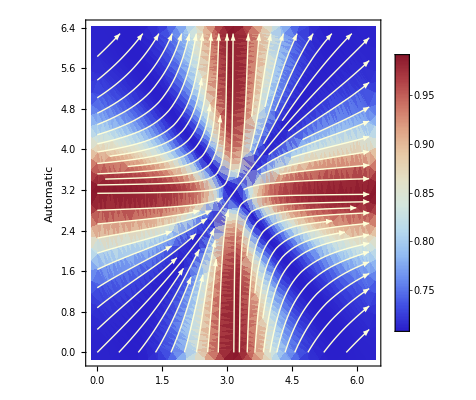

```mathematica
StreamDensityPlot[{P2DefQuantumNorm,P2CoopQuantumNorm},{θDef,0,2π},{θCoop,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{LightYellow, Thick},StreamScale->Full]
```

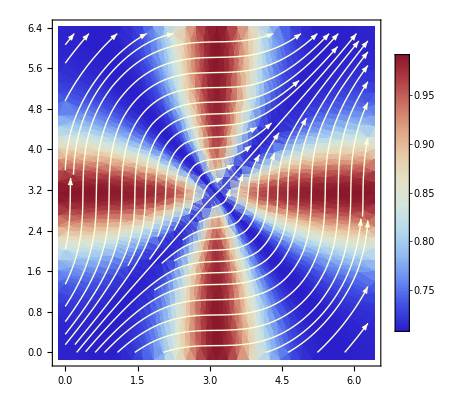

```mathematica
StreamDensityPlot[{P2CoopQuantumNorm,P2DefQuantumNorm},{θDef,0,2π},{θCoop,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,StreamStyle->{LightYellow, Thick},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},StreamScale->Full]
```

```mathematica
(* #################### DEFINING UTILITY STATES ###################### *)
```

```mathematica
(* Define the Utility node, U, as a matrix with the payoffs of the game *)
(* Player X2 wins 85 if he chooses defect when X1 also chose defect *)
(* Player X2 wins 85 if he chooses cooperate when X1 also chose defect *)
```

```mathematica
Udef = ({{dd, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, cd, 0}, {0, 0, 0, 0}});
```

```mathematica
UtilityX2d=Simplify[Total[Diagonal[P2DefQuantumNorm Udef]]]
```

(507.093+500. Cos[Re[θDef]])/(1.87812+0.847238 Cos[Re[θCoop]]+1. Cos[Re[θDef]])

```mathematica
(* ######### EXPECTED UTILITY OF DEFECTING ACCORDING TO THE QUANTUM-LIKE INFLUENCE DIAGRAMS ########## *)
```

```mathematica
utilDef = Plot3D[UtilityX2d,{θDef,0,2π},{θCoop,0,2π},ColorFunction->"DarkRainbow",AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Utility",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2, Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotStyle->Directive[Opacity[0.5],Red]]
```

-Graphics3D-

```mathematica
(* Player X2 wins 25 if he chooses defect when X1 also chose cooperate *)
(* Player X2 wins 75 if he chooses cooperate when X1 also chose cooperate *)
```

```mathematica
Ucoop = ({{0, 0, 0, 0}, {0, dc, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, cc}});
```

```mathematica
UtilityX2c=FullSimplify[Total[Diagonal[P2CoopQuantumNorm Ucoop]]]
```

(101.971+100. Cos[Re[θCoop]])/(2.21676+1. Cos[Re[θCoop]]+1.18031 Cos[Re[θDef]])

```mathematica
utilCoop = Plot3D[UtilityX2c,{θDef,0,2π},{θCoop,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Utility",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]]
```

-Graphics3D-

```mathematica
(* ######### EXPECTED UTILITY OF COOPERATION ACCORDING TO THE QUANTUM-LIKE INFLUENCE DIAGRAMS ########## *)
```

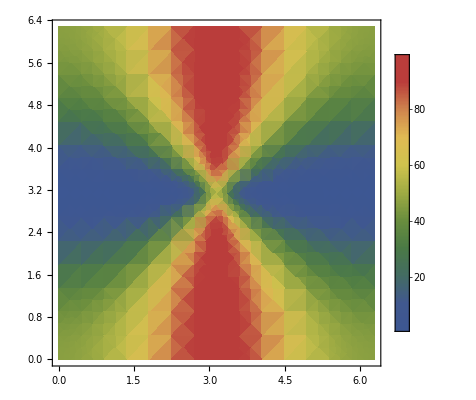

```mathematica
DensityPlot[UtilityX2c, {θDef,0,2π},{θCoop,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

```mathematica
(* ###### EXPECTED UTILITY OF COOPERATION AND DEFECT ACCORDING TO THE QUANTUM-LIKE INFLUENCE DIAGRAMS ####### *)
```

```mathematica
(* One can find that there are points in the graph that favour a cooperative action rather than a defect action *)
```

```mathematica
Show[utilCoop,utilDef,PlotRange->All]
```

-Graphics3D-

```mathematica
(* ############################# REGION PLOTS ############################################ *)
(* One can see in the above Figure that with quantum interference, one can influence the players' utilities in such a way that it favours a cooperative action. *)
```

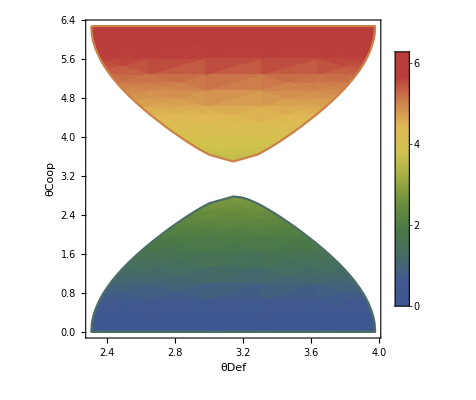

```mathematica
RegionPlot[UtilityX2c≥  UtilityX2d,{θDef,0,2π},{θCoop,0,2π},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

```mathematica
(* ############ ANALYSE EVOLUTION OF INTERFERENCE EFFECTS IN QUANTUM-LIKE EXPECTED UTILITIES ################ *)
```

```mathematica
(* Evolution of Decision-Makers beliefs to Defect towards beliefs to Cooperate *)
```

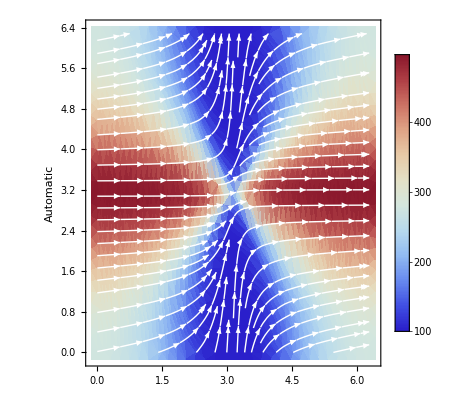

```mathematica
StreamDensityPlot[{UtilityX2d,UtilityX2c},{θDef,0,2π},{θCoop,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

```mathematica
(* Evolution of Decision-Makers beliefs to Cooperate towards beliefs to Defect *)
```

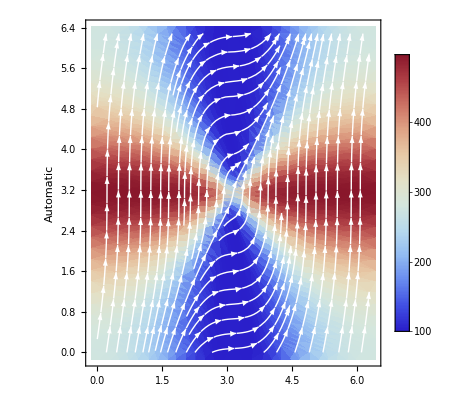

```mathematica
StreamDensityPlot[{UtilityX2c,UtilityX2d},{θDef,0,2π},{θCoop,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

## Evaluation of the Model in the Two Stage Gambling Game over Several Different Experiments of the Literature

```mathematica
Clear["Global`*"]
```

```mathematica
(* ############## DEFINING PATHS TO SAVE RESULTS ################################ *)
```

```mathematica
HOME = ""
```

```mathematica
(* ############## DEFINING PAYOFFS AND UTILITIES ################################ *)
(* we define the player's payoffs according to Table 2 *)
```

```mathematica
ww=400;  (* when player wins both gambles: $200 + $200 *)
wl=100;  (* when player wins first gamble, but loses second: $200 - $100 *)
lw=100;  (* when player loses first gamble, but wins second: -$100 + $200 *)
ll=-200;     (* when player loses both gambles: -$100 - $100 *)
```

```mathematica
(* ############## DEFINING PROBABILITY DISTRIBUTIONS FROM EXPERIMENTAL DATA ################################ *)
(* the conditional probability tables of the quantum-like Bayesian network are given by psychological experimental findings from the literature, which are presented in the above Table *)
```

```mathematica
pwp=0.63;            (* when player wins first gamble and plays second gamble *)
plp = 0.45;          (* when player loses first gamble and plays second gamble *)
pwnp = 1-pwp;   (* when player wins first gamble and does not play second gamble *)
plnp=1-plp;    (* when player loses first gamble and does not play second gamble *)
```

```mathematica
(* ############## DEFINING QUANTUM STATES ################################ *)
(* Each classical random variable corresponds to a Quantum State *)
(* Define the Quantum State |X1⟩ correspoding to the 1st player of the Prisoner's Dilemma *)
(* |X1⟩ = α1|X1=defect⟩ + α2|X1=cooperate⟩ *)
```

```mathematica
X1 =({{Sqrt[0.5]}, {Sqrt[0.5]}});
```

```mathematica
(* Define the Quantum Conditional Probability States |X2X1d⟩, |X2X1c⟩. Each state is defined in its own Hilbert Space *)
```

```mathematica
(*|X2X1⟩: Player 2 Prob. Amplitudes, given Player 1 is believed to have chosen Defect *)
(*        Player 2 Prob. Amplitudes given Player 1 is believed to have chosen Cooperate *)
```

```mathematica
X2X1=({{Sqrt[pwp] ⅇ^(ⅈ Re[θ1]), Sqrt[plp] ⅇ^(ⅈ Re[θ3])}, {Sqrt[pwnp] ⅇ^(ⅈ Re[θ2]), Sqrt[plnp] ⅇ^(ⅈ Re[θ4])}});
```

```mathematica
(* ######### COMPUTE THE FULL JOINT PROBABILITY DISTRIBUTION ######### *)
(* The goal is to create a quantum density matrix that corresponds to the product of the factors of the quantum states that represent the random variables of the QBN
 Joint = ∑_(i=1)^2 ∑_(j=1)^2 ∑_(k=1)^2 Subscript[α, i] Subscript[β, j1] Subscript[β, k2]|X1 = i ⊗ X2X1d = j ⊗ X2X1c = k ⟩ *)
```

```mathematica
J=ConstantArray[0,{4}];
For[c=1;i=1,i≤2,i++,
For[j=1,j≤2,j++,
J[[c]]=X1[[i]] X2X1[[j,i]];
c=c+1;
]];
```

```mathematica
(* Simplify Joint generate density matrix from product of factors (or product of quantum states *)
```

```mathematica
(* Joint = |J⟩⟨J| *)
```

```mathematica
Joint = FullSimplify[J . ConjugateTranspose[J]];
```

```mathematica
MatrixForm[Joint]
```

(0.315 | 0.241402 ⅇ^(ⅈ Re[θ1-θ2]) | 0.266224 ⅇ^(ⅈ Re[θ1-θ3]) | 0.294321 ⅇ^(ⅈ Re[θ1-θ4])
0.241402 ⅇ^(-ⅈ Re[θ1-θ2]) | 0.185 | 0.204022 ⅇ^(ⅈ Re[θ2-θ3]) | 0.225555 ⅇ^(ⅈ Re[θ2-θ4])
0.266224 ⅇ^(-ⅈ Re[θ1-θ3]) | 0.204022 ⅇ^(-ⅈ Re[θ2-θ3]) | 0.225 | 0.248747 ⅇ^(ⅈ Re[θ3-θ4])
0.294321 ⅇ^(-ⅈ Re[θ1-θ4]) | 0.225555 ⅇ^(-ⅈ Re[θ2-θ4]) | 0.248747 ⅇ^(-ⅈ Re[θ3-θ4]) | 0.275)

```mathematica
(* Check if calculations are correct. The classical full joint distribution should correspond to the sum of all diagonal elements of the density matrix *)
```

```mathematica
If[Total[Diagonal[Joint]] == 1,
Print[Correct!],
Print[Error! ]]
```

Correct!

```mathematica
(* ################ Generate Quantum-Like Inferences ##################### *)
(* The goal is to create an operator that selects the entries in the density matrix that correspond to a specifc query *)
(* OPERATORS: *)
(* X1 X2 | Pr( X1, X2 ) *)
(* ------------------------------ *)
(* D  D  | Pr(X1=D) Pr(X2=D|X1=D) *)
(* D  C  | Pr(X1=D) Pr(X2=C|X1=C) *)
(* C  D  | Pr(X1=C) Pr(X2=D|X1=D) *)
(* C  C  | Pr(X1=C) Pr(X2=D|X1=C) *)
```

```mathematica
(* Play Gamble: computed just like in the classical setting. Select the 1st and 3rd position of the classical joint *)
```

```mathematica
PlayG= ({{1}, {0}, {1}, {0}});
```

```mathematica
(* Not Play Gamble: computed just like in the classical setting. Select the 2nd and 4th position of the classical joint *)
```

```mathematica
NotPlayG= ({{0}, {1}, {0}, {1}});
```

```mathematica
(* CLASSICAL: *)
```

```mathematica
(* Compute Pr( P2 = defect ) = Trace[ Defect' Joint Defect ] = 0.905 *)
```

```mathematica
P2PlayClassical =(Transpose[PlayG].Diagonal[Joint ] )[[1]]
```

0.54

```mathematica
(* Compute Pr( P2 = play ) = Trace[ Cooperate Joint ] = 0.095 *)
```

```mathematica
P2NotPlayClassical =  (Transpose[NotPlayG].Diagonal[Joint ] )[[1]]
```

0.46

```mathematica
(* QUANTUM: *)
```

```mathematica
(* PARTIAL TRACE FUCNTION *)
```

```mathematica
(* Compute Pr( P2 = defect ) =  α|Defect Joint|^2  = 0.905 + Int. *)
```

```mathematica
(* where α is a normalization factor that corresponds to: Pr( P2 = defect ) + Pr( P2 = coop ) *)
```

```mathematica
P2PlayQuantum= FullSimplify[Transpose[PlayG] . Joint. PlayG, θPlay== θ1- θ3][[1]][[1]]
```

0.54+0.532447 Cos[Re[θPlay]]

```mathematica
(* Compute Pr( P2 = cooperate ) =  |Cooperate Joint|^2  = 0.095 + Int. *)
```

```mathematica
P2NotPlayQuantum = FullSimplify[Transpose[NotPlayG] . Joint. NotPlayG,θNotPlay == θ2-θ4][[1]][[1]]
```

0.46+0.45111 Cos[Re[θNotPlay]]

```mathematica
(* Normalize Results *)
```

```mathematica
Normalization[x_,y_]:=x/(x+y)
```

```mathematica
(* Quantum probability of defecting *)
```

```mathematica
P2PlayQuantumNorm = Normalization[P2PlayQuantum,P2NotPlayQuantum]
```

(0.54+0.532447 Cos[Re[θPlay]])/(1.+0.45111 Cos[Re[θNotPlay]]+0.532447 Cos[Re[θPlay]])

```mathematica
(* Quantum probability of cooperating *)
```

```mathematica
P2NotPlayQuantumNorm= Normalization[P2NotPlayQuantum,P2PlayQuantum]
```

(0.46+0.45111 Cos[Re[θNotPlay]])/(1.+0.45111 Cos[Re[θNotPlay]]+0.532447 Cos[Re[θPlay]])

```mathematica
(* ######### QUANTUM PROBABILITY OF COOPERATING ACCORDING TO DIFFERENT INTERFERENCES ########## *)
```

```mathematica
qProbNotPlay= Plot3D[P2NotPlayQuantumNorm,{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Play",16],Style["θ_NotPlay",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]]
```

-Graphics3D-

```mathematica
(* ######### QUANTUM PROBABILITY OF DEFECTING ACCORDING TO DIFFERENT INTERFERENCES ########## *)
```

```mathematica
qProbPlay = Plot3D[P2PlayQuantumNorm,{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Play",16],Style["θ_NotPlay",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotStyle->Directive[Opacity[0.2],Red]]
```

-Graphics3D-

```mathematica
(* Plot both graphs *)
```

```mathematica
Show[qProbNotPlay,qProbPlay,PlotRange->All]
```

-Graphics3D-

```mathematica
StreamDensityPlot[{P2PlayQuantumNorm,P2NotPlayQuantumNorm},{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{LightYellow, Thick},StreamScale->Full]
```

-Graphics-

```mathematica
StreamDensityPlot[{P2NotPlayQuantumNorm,P2PlayQuantumNorm},{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,StreamStyle->{LightYellow, Thick},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},StreamScale->Full]
```

-Graphics-

```mathematica
(* #################### DEFINING UTILITY STATES ###################### *)
```

```mathematica
(* Define the Utility node, U, as a matrix with the payoffs of the game *)
(* Player X2 wins 85 if he chooses defect when X1 also chose defect *)
(* Player X2 wins 85 if he chooses cooperate when X1 also chose defect *)
```

```mathematica
Uplay = ({{ww, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, lw, 0}, {0, 0, 0, 0}});
```

```mathematica
UtilityX2p=Simplify[Total[Diagonal[P2PlayQuantumNorm Uplay]]]
```

(507.093+500. Cos[Re[θPlay]])/(1.87812+0.847238 Cos[Re[θNotPlay]]+1. Cos[Re[θPlay]])

```mathematica
(* ######### EXPECTED UTILITY OF DEFECTING ACCORDING TO THE QUANTUM-LIKE INFLUENCE DIAGRAMS ########## *)
```

```mathematica
utilPlay = Plot3D[UtilityX2p,{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->"DarkRainbow",AxesLabel->{Style["θ_Play",16],Style["θ_NotPlay",16],Style["Utility",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2, Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotStyle->Directive[Opacity[0.5],Red]]
```

-Graphics3D-

```mathematica
(* Player X2 wins 25 if he chooses defect when X1 also chose cooperate *)
(* Player X2 wins 75 if he chooses cooperate when X1 also chose cooperate *)
```

```mathematica
UnotPlay = ({{0, 0, 0, 0}, {0, wl, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, ll}});
```

```mathematica
UtilityX2np=FullSimplify[Total[Diagonal[P2NotPlayQuantumNorm UnotPlay]]]
```

(-101.971-100. Cos[Re[θNotPlay]])/(2.21676+1. Cos[Re[θNotPlay]]+1.18031 Cos[Re[θPlay]])

```mathematica
utilNotPlay = Plot3D[UtilityX2np,{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Play",16],Style["θ_NotPlay",16],Style["Utility",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]]
```

-Graphics3D-

```mathematica
(* ######### EXPECTED UTILITY OF COOPERATION ACCORDING TO THE QUANTUM-LIKE INFLUENCE DIAGRAMS ########## *)
```

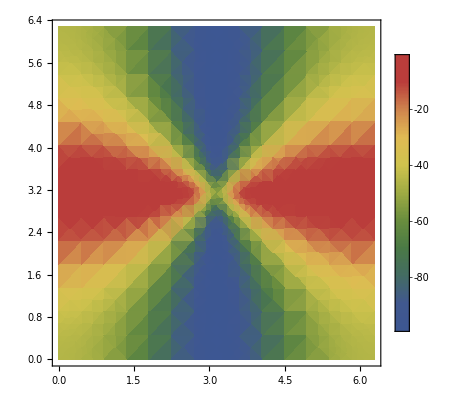

```mathematica
DensityPlot[UtilityX2np, {θPlay,0,2π},{θNotPlay,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

```mathematica
(* ###### EXPECTED UTILITY OF COOPERATION AND DEFECT ACCORDING TO THE QUANTUM-LIKE INFLUENCE DIAGRAMS ####### *)
```

```mathematica
(* One can find that there are points in the graph that favour a cooperative action rather than a defect action *)
```

```mathematica
Show[utilNotPlay,utilPlay,PlotRange->All]
```

-Graphics3D-

```mathematica
(* ############################# REGION PLOTS ############################################ *)
(* One can see in the above Figure that with quantum interference, one can influence the players' utilities in such a way that it favours a cooperative action. *)
```

```mathematica
RegionPlot[UtilityX2np≥  UtilityX2p,{θPlay,0,2π},{θNotPlay,0,2π},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

-Graphics-

```mathematica
(* ############ ANALYSE EVOLUTION OF INTERFERENCE EFFECTS IN QUANTUM-LIKE EXPECTED UTILITIES ################ *)
```

```mathematica
(* Evolution of Decision-Makers beliefs to Defect towards beliefs to Cooperate *)
```

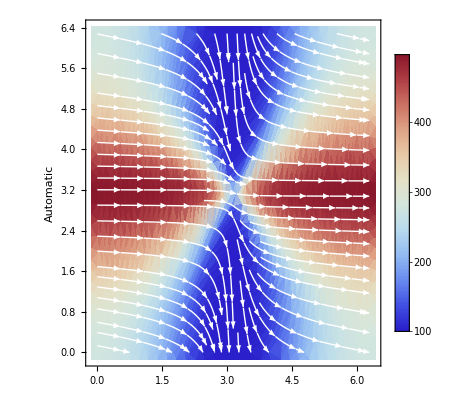

```mathematica
StreamDensityPlot[{UtilityX2p,UtilityX2np},{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

```mathematica
(* Evolution of Decision-Makers beliefs to Cooperate towards beliefs to Defect *)
```

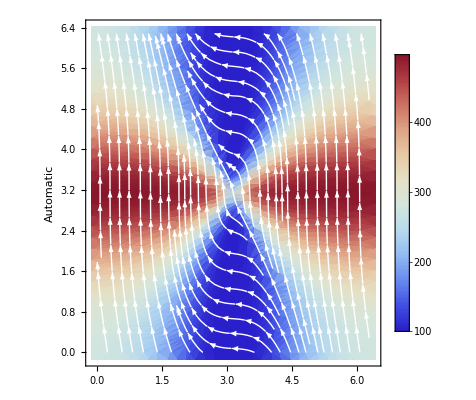

```mathematica
sp2=StreamDensityPlot[{UtilityX2np,UtilityX2p},{θPlay,0,2π},{θNotPlay,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

```mathematica
(* Save image *)
```

```mathematica
Export["exportP1.png",sp2]
```

exportP1.png

```mathematica
HOME =
```

./Desktop/

```mathematica
FILE = "Shafir_Tversky(1992)_2"
```

Shafir_Tversky(1992)_2

```mathematica
"Shafir_Tversky(1992)_v2"
```

Shafir_Tversky(1992)_v2

```mathematica
EXT = ".png"
```

.png

```mathematica
str = StringJoin[HOME,FILE,EXT]
```

./Desktop/Shafir_Tversky(1992)_2.png

```mathematica
Export[str,sp2, ImageResolution-> 200]
```

./Desktop/Shafir_Tversky(1992)_2.png